CreateDirectory::filex: "C:\\Users\\Petr\\Desktop\\Projects\\Programming Techniques\\shown results\\hash\\" already exists.

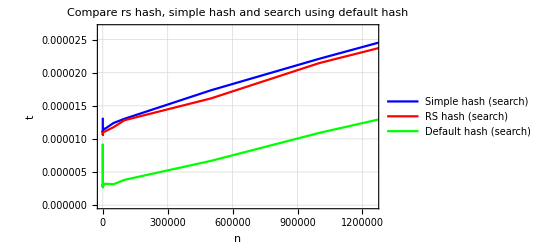

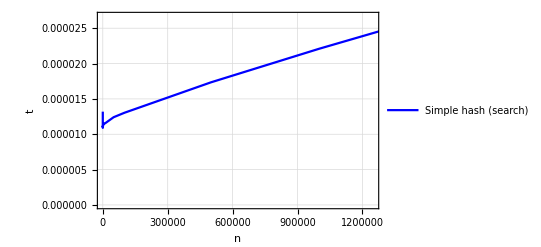

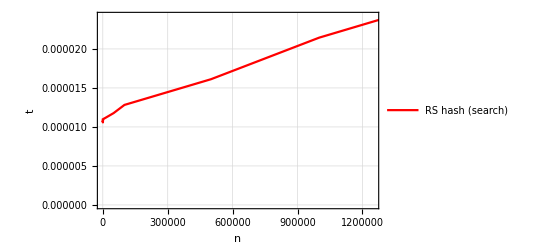

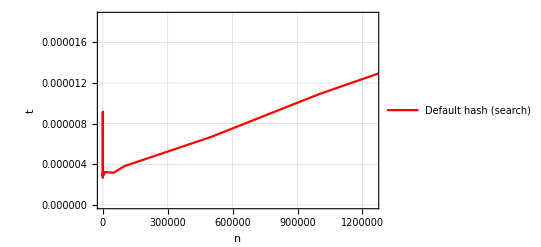

```mathematica
SetDirectory[NotebookDirectory[]];
workingDirectory = "../shown results";
SetDirectory[workingDirectory];
file= OpenRead["../logs/log_hash.txt"];
workingDirectory = CreateDirectory["hash"];
SetDirectory[workingDirectory];
filelist= ReadList[file,String];

defaultSearchResults = filelist[[3;;;;4]];
rsSearchResults = filelist[[2;;;;4]];
simpleSearchResults = filelist[[1;;;;4]];
simpleSearchResults= Map[({StringSplit[#][[4]],StringSplit[#][[7]]})&,simpleSearchResults];
rsSearchResults= Map[({StringSplit[#][[4]],StringSplit[#][[7]]})&,rsSearchResults];
defaultSearchResults= Map[({StringSplit[#][[4]],StringSplit[#][[7]]})&,defaultSearchResults];
simpleSearchResults= Map[({Read[StringToStream[#[[1]]],Number],Read[StringToStream[#[[2]]],Number]})&,simpleSearchResults];
rsSearchResults= Map[({Read[StringToStream[#[[1]]],Number],Read[StringToStream[#[[2]]],Number]})&,rsSearchResults];
defaultSearchResults= Map[({Read[StringToStream[#[[1]]],Number],Read[StringToStream[#[[2]]],Number]})&,defaultSearchResults];
Plot1 = Show[ListPlot[simpleSearchResults,Joined->True,PlotStyle->Blue,PlotLegends->{"Simple hash (search)"},PlotLabel->"Compare rs hash, simple hash and search using default hash", AxesLabel->{"n","t"},PlotTheme->"Detailed",ImageSize->Scaled[0.8]],ListPlot[rsSearchResults,Joined->True,PlotStyle->Red,PlotLegends->{"RS hash (search)"}],
ListPlot[defaultSearchResults,Joined->True,PlotStyle->Green,PlotLegends->{"Default hash (search)"}]]
Plot2 = ListPlot[simpleSearchResults,Joined->True,PlotStyle->Blue,PlotLegends->{"Simple hash (search)"}, AxesLabel->{"n","t"},PlotTheme->"Detailed",ImageSize->Scaled[0.8]]
Plot3 = ListPlot[rsSearchResults,Joined->True,PlotStyle->Red,PlotLegends->{"RS hash (search)"}, AxesLabel->{"n","t"},PlotTheme->"Detailed",ImageSize->Scaled[0.8]]
Plot4 = ListPlot[defaultSearchResults,Joined->True,PlotStyle->Red,PlotLegends->{"Default hash (search)"},AxesLabel->{"n","t"},PlotTheme->"Detailed",ImageSize->Scaled[0.8]]
```

```mathematica
Export["Comp1.gif",Plot1,ImageSize->2048];
Export["Simple.gif",Plot2,ImageSize->2048];
Export["RS.gif",Plot3,ImageSize->2048];
Export["Default.gif",Plot4,ImageSize->2048];
```

```mathematica
grid = Grid[Transpose[{Join[{"Number"},rsSearchResults[[All,1]]],Join[{"Simple hash (search) sec."},simpleSearchResults[[All,2]]],Join[{"RS hash (search) sec."},rsSearchResults[[All,2]]],Join[{"Default hash (search) sec."},defaultSearchResults[[All,2]]]}],Frame->All,Alignment->Left,Background->{None,{Yellow}},ItemStyle->Directive[FontSize->20,Bold]]
```

Number | Simple hash (search) sec. | RS hash (search) sec. | Default hash (search) sec.
5 | 0.0000131961 | 0.0000110738 | 3.14141×10^-6
10 | 0.0000111031 | 0.0000110224 | 2.89215×10^-6
50 | 0.0000111581 | 0.0000106815 | 2.80418×10^-6
100 | 0.0000109051 | 0.0000107255 | 9.16765×10^-6
500 | 0.0000110957 | 0.0000105826 | 2.67588×10^-6
1000 | 0.0000111837 | 0.0000108795 | 3.23672×10^-6
5000 | 0.0000115393 | 0.0000110628 | 2.97646×10^-6
10000 | 0.000011532 | 0.0000111287 | 3.23305×10^-6
50000 | 0.000012408 | 0.0000117739 | 3.16707×10^-6
100000 | 0.0000130385 | 0.0000128222 | 3.81955×10^-6
500000 | 0.0000173456 | 0.0000161176 | 6.68971×10^-6
1000000 | 0.0000220962 | 0.0000214474 | 0.0000109088
5000000 | 0.0000576818 | 0.0000544487 | 0.0000404828

```mathematica
Export["TableHash.gif",grid,ImageSize->{2048,720}];
Export["TableHash.xls",grid,ImageSize->{2048,720}];
```